```mathematica
A=Outer[Times,{1,0,1,0},{1,0,1,0}]+Outer[Times,{0,1,0,1},{0,1,0,1}]//MatrixForm
```

(1 | 0 | 1 | 0
0 | 1 | 0 | 1
1 | 0 | 1 | 0
0 | 1 | 0 | 1)

```mathematica
B={{0,0,1,0},{0,0,0,1},{1,0,0,0},{0,1,0,0}}+DiagonalMatrix[{1,1,1,1}]//MatrixForm
```

(1 | 0 | 1 | 0
0 | 1 | 0 | 1
1 | 0 | 1 | 0
0 | 1 | 0 | 1)

```mathematica
A+B
```

2 (1 | 0 | 1 | 0
0 | 1 | 0 | 1
1 | 0 | 1 | 0
0 | 1 | 0 | 1)

```mathematica
II={{1,0},{0,1}};zero={{0,0},{0,0}};sig1={{0,1},{1,0}};sig2={{0,-I},{I,0}};sig3={{1,0},{0,-1}};
```

```mathematica
g0={{II,zero},{zero,II}}
```

{{{{1,0},{0,1}},{{0,0},{0,0}}},{{{0,0},{0,0}},{{1,0},{0,1}}}}

```mathematica
Table[Integrate[x^n*Exp[-x],{x,0,Infinity},Assumptions->Re[n]>-1]/Factorial[n],{n,0,5}]
```

{1,1,1,1,1,1}

```mathematica
Expand[(q2+M2^2-M4^2)^2]
```

M2^4-2 M2^2 M4^2+M4^4+2 M2^2 q2-2 M4^2 q2+q2^2

```mathematica
Integrate[1/(Exp[x-Eta]+1),{x,0,Infinity}]
```

Log[1+ⅇ^Eta]

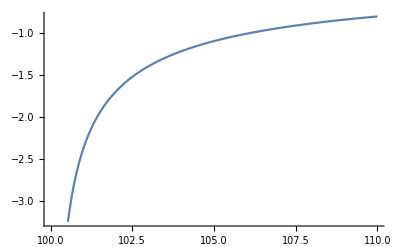

```mathematica
Plot[-x/(3*Sqrt[x^2-100^2]),{x,100,110}]
```

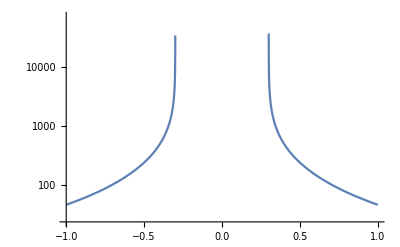

```mathematica
LogPlot[(Q^2 q0 β+√(mu^2 q^2 (m2^2 ((-2+4 mu^2) q^2-2 (Q^2+q0^2))+Q^4 β^2)))/(2 mu^2 q^2-2 q0^2)-m2,{mu,-1,1},PlotRange->All]
```

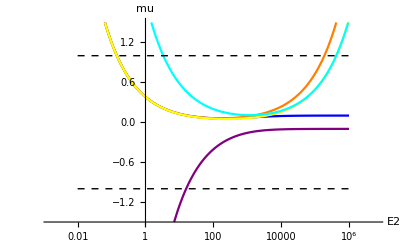

```mathematica
q=30;q0=0.1q;Q=Sqrt[q0^2-q^2];m2=939;m4=941;β=1+(m2^2-m4^2)/(q0^2-q^2);LogLinearPlot[{(2 (E2+m2) q0+Q^2 β)/(2 √((E2+m2)^2-m2^2) q),(2 (E2+m2) q0+Q^2 β)/(2 (Sqrt[2*E2*m2] )q),(-2 (E2+m2) q0+Q^2 β)/(2 √((E2+m2)^2-m2^2) q),-(2 E2 (m2-m4)-2 m2 m4+2 m4^2+q^2-2 m4 q0)/(2 √2 √(E2 m2) q),-(2 E2 (m2-m4)+q^2-2 m4 q0)/(2 √2 √(E2 m2) q),1,-1},{E2,10^-2,10^6},PlotRange->{-1.5,1.5},AxesLabel->{E2,mu},AxesOrigin->{1,-1.5},PlotStyle->{Blue,Orange,Purple,Yellow,Cyan,{Black,Dashed,Thin},{Black,Dashed,Thin}}]
```

```mathematica
(Q^2 q0 β+√(mu^2 q^2 (m2^2 ((-2+4 mu^2) q^2-2 (Q^2+q0^2))+Q^4 β^2)))/(2 mu^2 q^2-2 q0^2)//.{mu->0.1}
```

17.0625-353.508 ⅈ

```mathematica
f[mu_,E2_]:=q0+E2-Sqrt[E2^2-m2^2+m4^2+q^2+2Sqrt[E2^2-m2^2]q*mu];Simplify[Solve[f[mu,E2]==0,mu]]
```

{{mu→(m2^2-m4^2-q^2+2 E2 q0+q0^2)/(2 √(E2^2-m2^2) q)}}

```mathematica
Simplify[Solve[(p2^2+q^2+2p2*q*mu)/(2m4)+m4==q0+p2^2/(2m2)+m2,mu]//.{p2->Sqrt[2m2*(E2-m2)]}]
```

{{mu→-(-2 m2^2+2 E2 (m2-m4)+2 m4^2+q^2-2 m4 q0)/(2 √2 √((E2-m2) m2) q)}}

```mathematica
Clear[mu,q0,p2,m2,q,m4,x];Simplify[Simplify[mu/.Solve[q0+p2^2/(2*m2)==(p2^2+q^2+2*p2*q*mu)/(2m4),mu]][[1]]]
```

(m4 p2^2-m2 (p2^2+q^2-2 m4 q0))/(2 m2 p2 q)

```mathematica
FullSimplify[(p2/.Simplify[Solve[(m4 p2^2-m2 (p2^2+q^2-2 m4 q0))/(2 m2 p2 q)==1,p2]][[1]])^2//.{m2->(1-x)/m4}]
```

((q+m4 √(((-m4 q^2+2 m4^2 q0+2 q0 (-1+x)) (-1+x))/m4)-q x)^2)/((-1+m4^2+x)^2)